```mathematica
(*

Copyright (c)2018 Erik Grumstrup

Permission is hereby granted,free of charge,to any person obtaining a copy of this software and associated documentation files (the "Software"),to deal in the Software without restriction including without limitation the rights to use,copy,modify,merge,publish,distribute,sublicense,and/or sell copies of the Software and to permit persons to whom the Software is furnished to do so subject to the following conditions: The above copyright notice and this permission notice shall be included in all copies or substantial portions of the Software.

THE SOFTWARE IS PROVIDED "AS IS",WITHOUT WARRANTY OF ANY KIND,EXPRESS OR IMPLIED,INCLUDING BUT NOT LIMITED TO THE WARRANTIES OF MERCHANTABILITY,FITNESS FOR A PARTICULAR PURPOSE AND NONINFRINGEMENT. IN NO EVENT SHALL THE AUTHORS OR COPYRIGHT HOLDERS BE LIABLE FOR ANY CLAIM,DAMAGES OR OTHER LIABILITY, WHETHER IN AN ACTION OF CONTRACT,TORT OR OTHERWISE,ARISING FROM, OUT OF OR IN CONNECTION WITH THE SOFTWARE OR THE USE OR OTHER DEALINGS IN THE SOFTWARE.

*)
```

```mathematica
Clear["Global`*"]
```

```mathematica
{FileNameSetter[Dynamic[rfile]],Dynamic[rfile]}(*nucleus outline file*)
{FileNameSetter[Dynamic[ROIfile]],Dynamic[ROIfile]}(*ROI definition file*)
{FileNameSetter[Dynamic[kfile]],Dynamic[kfile]}(*kinetics file from experiment*)
```

{$CellContext`rfileOpenAll,}

{$CellContext`ROIfileOpenAll,}

{$CellContext`kfileOpenAll,}

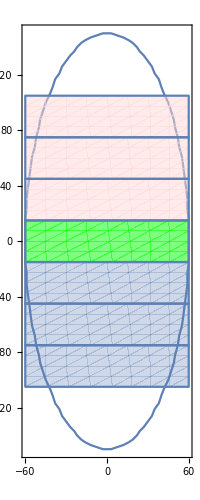

```mathematica
t0=10.5;(*time offset so that model and exp data can be on same time axis*)
columnstart=9;(*starting column of data you want from kintics file*)
columnend=15;(*ending column of data you want from kintics file*)
exptime=Import[kfile,"CSV"][[5;;All,1]]; (*strips some header info from top of file*)
exptime=exptime-t0;
expdata=Import[kfile,"CSV"][[5;;All,columnstart;;columnend]];
expdata=Table[expdata[[;;,i]]/Mean[expdata[[1;;6,i]]],{i,1,Dimensions[expdata][[2]]}]ᵀ(*normalize data to first 6 frames*);expdata=Table[{exptime,expdata[[;;,i]]}ᵀ,{i,1,Dimensions[expdata][[2]]}];
rdat=Import[rfile,"CSV"];
ROIcoords=Import[ROIfile,"CSV"][[1,;;]];(*import coordinates for ROI0*)
rdat={rdat[[;;,2]],rdat[[;;,1]]}ᵀ;
rdat[[Length[rdat]]]=rdat[[1]];(*sets last point == to first point so that the region is bounded*)
r1=BoundaryDiscretizeGraphics@ListLinePlot[rdat];(*define region in mathematica language*)
com=RegionCentroid[r1];(*find the center of the region*)
rdat=Table[rdat[[i]]-com,{i,1,Length[rdat]}];(*move coords so that COM is at 0,0*)
rdat=Round[rdat];(*round to integers*)
r2=BoundaryDiscretizeGraphics@ListLinePlot[rdat];(*make new region to be used for simulation, centered at 0,0 and comprised of integer values*)
ROIcoords[[1]]=ROIcoords[[1]]-Round[com[[1]]];
ROIcoords[[2]]=ROIcoords[[2]]-Round[com[[2]]];

(*define ROIs*)
ROIn=Table[Region[Rectangle[{ROIcoords[[1]],ROIcoords[[2]]+i*ROIcoords[[4]]},{ROIcoords[[1]]+ROIcoords[[3]],ROIcoords[[2]]+(i+1)*ROIcoords[[4]]}]],{i,1,3}];
ROI0=Region[Rectangle[{ROIcoords[[1]],ROIcoords[[2]]},{ROIcoords[[1]]+ROIcoords[[3]],ROIcoords[[2]]+ROIcoords[[4]]}]];
ROIp=Table[Region[Rectangle[{ROIcoords[[1]],ROIcoords[[2]]-i*ROIcoords[[4]]},{ROIcoords[[1]]+ROIcoords[[3]],ROIcoords[[2]]-(i-1)*ROIcoords[[4]]}]],{i,1,3}];
ROIlims=Table[{{ROIcoords[[1]],ROIcoords[[2]]+i*ROIcoords[[4]]},{ROIcoords[[1]]+ROIcoords[[3]],ROIcoords[[2]]+(i+1)*ROIcoords[[4]]}},{i,-3,3}];

Show[RegionPlot[r2,AspectRatio->Automatic,PlotRange->{{-200,200},{200,-200}}],RegionPlot[ROI0,PlotStyle->{Green,Opacity[0.5]}],RegionPlot[ROIn[[1]],PlotStyle->{LightRed,Opacity[0.5]}],RegionPlot[ROIn[[2]],PlotStyle->{LightRed,Opacity[0.5]}],RegionPlot[ROIn[[3]],PlotStyle->{LightRed,Opacity[0.5]}],RegionPlot[ROIp[[1]]],RegionPlot[ROIp[[2]]],RegionPlot[ROIp[[3]]]]
```

```mathematica
(*Show[RegionPlot[r2,AspectRatio->Automatic,BoundaryStyle->{Black,Thick},PlotRange->{{-90,90},{-150,150}}],Graphics[{PointSize->Tiny,Blue,Point[RandomPoint[r2,12000]]}]]*)
```

```mathematica
mparp=1000;(*out of a 1000, how many parps are mobile?*)
scale=0.08677;(*sets scale of pixel in microns*)
timestep=.12045;(*sets time step in seconds*)
nsteps=550;(*number of time steps - total simulation time is nsteps*timestep*)
npoints=5000;(*number of particles*)
limhi=100+50;(*arbitrary limit for plotting*)
meanD1=12;(*mean step size*)
stddevD1=.001;(*std deviation of diffusion constant distribution*)
D1:=Round[RandomVariate[NormalDistribution[meanD1,stddevD1]]];(*step size in pixels*)
(simtime=timestep*nsteps) "seconds of simulation time"
(scaledD=(1/2)*meanD1^2*scale^2*(1/timestep)) "μm^2/s" (*diffusion constant, assumes equal probability of Left or Right at each step, same for Up or down*)
BleachFraction=1.;(*fraction remaining unbleached in ROI0*)
If[stddevD1>.1,Plot[PDF[NormalDistribution[scaledD,(stddevD1/meanD1)scaledD],x],{x,-scaledD,3 scaledD},PlotRange->All,Frame->True,FrameLabel->{"D (um^2/s)","Intensity (arb. units)"},LabelStyle->{FontFamily->"Arial",14,Black},FrameStyle->Black]](*plots distribution of diffusion consnants if there is appreciable width*)
pointpic:=Catenate[{Round[RandomPoint[r2]],{0},{D1}}];(*picks random points in region defining nucleus. Format is {x pos, y pos, step index, step size}*)
Prop[ts_]:=Module[{t1=ts,t0},
t0=t1;
If[!(ROIlims[[4,1,2]]<t1[[2]]<=ROIlims[[4,2,2]]),(*conditional (not!) test if points lie inside ROI0*)(*true case*)
t1[[1;;2]]+={t1[[4]]*RandomChoice[{-1,1}],t1[[4]]*RandomChoice[{-1,1}]};(*hop step*)
If[RegionMember[r2,t1[[1;;2]]],t1,t1=t0] (*maintains boundary conditions of nucleus*)
];
t1[[3]]+=1;
t1
](*function that propagates each particle a step*)
```

66.2475 seconds of simulation time

4.50054 μm^2/s

{5000,551,4}

{24.034,Null}

-667.21

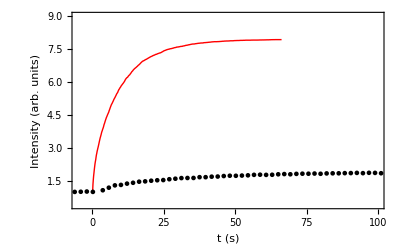

```mathematica
trajmobile=ParallelTable[NestList[Prop,pointpic,nsteps],{Round[npoints*mparp/1000]}];(*calculate trajectories for npoints particles*)
traj=Catenate[{trajmobile,Table[p=pointpic;(Table[p,nsteps+1]),Round[npoints*(1-mparp/1000)]]}];(*catenates mobile trajectories with fixed trajectories*)
Dimensions[traj]
kinROI=ParallelTable[
xlim1=ROIlims[[k,1,1]];
xlim2=ROIlims[[k,2,1]];
ylim1=ROIlims[[k,1,2]];
ylim2=ROIlims[[k,2,2]];
trap=Total[Table[If[xlim1<traj[[i,j,1]]<xlim2 &&ylim1<traj[[i,j,2]]<=ylim2 ,1,0],{i,1,npoints},{j,1,nsteps}],{1}];
If[k==4,
If[trap[[1]]≠0,
trap[[2;;All]]=trap[[2;;All]]-Round[(1-BleachFraction)*trap[[1]]];
trap=trap/trap[[1]];
];
];
Table[{i*timestep,trap[[i]]},{i,1,Length[trap]}],
{k,1,7}];//AbsoluteTiming(*this loop counts all the particles in each ROI*)

(*start R^2 subsection*)
	SSres=0;
	SStot=0;
	i=Length[Select[expdata[[4,;;,1]],#<0&]]+1;(*finds number of points before t =0*)
	i0=i;
	mean=0;
	siminterp=Interpolation[kinROI[[4]]];
	While[expdata[[4,i,1]]≤simtime,
	SSres+=(expdata[[4,i,2]]-siminterp[expdata[[4,i,1]]])^2;
	mean+=expdata[[4,i,2]];
	i++;
	](*sums mean and residuals for times between t = 0 and simtime*) 
	mean=mean/(i-i0-1);
	i=i0;
	While[expdata[[4,i,1]]≤simtime,
	SStot+=(expdata[[4,i,2]]-mean)^2;
	i++;
	]
	( 1-SSres/SStot) 
(*end R^2 subsection*)

GraphicsRow[{ListLinePlot[{kinROI[[4]],expdata[[4]]},Frame->True,FrameLabel->{"t (s)","Intensity (arb. units)"},LabelStyle->{FontFamily->"Arial",18,Black},FrameStyle->Black,PlotRange->{{-5,100},{.4,9}},PlotStyle->{{Red,Thick},{Black,Dashed}},Joined->{True,False}]
(*,ListLinePlot[{kinROI[[1]],kinROI[[2]],kinROI[[3]],expdata[[1]],expdata[[2]],expdata[[3]]},AspectRatio->1,Frame->True,FrameLabel->{"t (s)","Intensity (arb. units)"},LabelStyle->{FontFamily->"Arial",18,Black},FrameStyle->Black,PlotRange->{{-5,100},{.4,1.1}},Joined->True,PlotStyle->{{Red,Thick},{Blue,Thick},{Black,Thick},{Red,Dashed},{Blue,Dashed},{Black,Dashed}}]*)}](*solid lines are simulation data, dashed lines are experimental data*)
```

```mathematica
exportsimdata=N[Table[Catenate[{kinROI[[1,i,;;]],kinROI[[2,i,;;]],kinROI[[3,i,;;]],kinROI[[4,i,;;]],kinROI[[5,i,;;]],kinROI[[6,i,;;]],kinROI[[7,i,;;]]}],{i,1,nsteps}]]; (*writes array of simulation data for export*)
```

```mathematica
Export["difftest_5.txt",exportsimdata1,"TSV"](*need to specifiy the filename - the part in quotes - this saves by default into your home directory*)
```

difftest_5.txt